### Categorization

Tutorial

QNMspectral

QNMspectral`

QNMspectral/tutorial/TechnicalDetails

### Keywords

Details

# Method

## Boundary Conditions and Eddington-Finkelstein coordinates

To find the quasinormal mode spectrum, we have to solve for a linearized perturbation on top of a black hole/black brane, with ingoing boundary conditions at the horizon, and normalizability at the boundary.

It turns out that Eddington-Finkelstein coordinates are perfectly suited for this problem. By Eddington-Finkelstein coordinates we mean more specifically a metric of the form

ds^2=-f(r) dt^2+2g(r) dt dr (+ spatial part), where f(r) is the blackening factor, and g(r) depends on the gauge of the radial variable.

Consider the simple example of a massless scalar field in a 5-dimensional Schwarschild-AdS black brane, which can be written as

```mathematica
eqϕ=-6 ⅈ λ δϕ[u]+(-3-u^4+4 ⅈ u λ) δϕ'[u]+(u-u^5) δϕ''[u];
```

Here u=0 is the boundary and u=1 the horizon, corresponding to a gauge where g(u)=-1/u^2, and λ=ω/4π T, with ω the frequency of the perturbation and T the temperature of the black brane.

Near the horizon there are two solutions,

```mathematica
Series[(1-u)^-p eqϕ/.δϕ->(u↦(1-u)^p)//Expand,{u,1,-1}]
Solve[Normal[%]==0,p]
```

(-4 p^2+4 ⅈ p λ)/(u-1)+O[u-1]^0

{{p→0},{p→ⅈ λ}}

One goes to a constant, and the other behaves as δϕ(u)~(1-u)^(i λ).

Including time dependence, this last solution behaves as δϕ(t,u)= e^(-i λ (4 π t T-(1-u) log)), so as t increases, 1-u has to increase as well to keep a constant phase, meaning u has to decrease, so this solution corresponds to an outgoing wave. The other solution going to a constant must then correspond to an ingoing wave.

Notice that the solution that we want, the ingoing one, is perfectly smooth, while the one we want to discard, the outgoing one, oscillates more and more rapidly as we approach the horizon. These properties will help us pick out the correct solution, as we will see in the next section.

The boundary is more straightforward, again there are two solutions, now corresponding to a normalizable and a non-normalizable mode:

```mathematica
Series[(u)^-p eqϕ/.δϕ->(u↦u^p)//Expand,{u,0,-1}]
Solve[Normal[%]==0,p]
```

(-4 p+p^2)/u+O[u]^0

{{p→0},{p→4}}

The solution going to a constant is the non-normalizable mode, while the one going like  δϕ(u)~u^4 is the normalizable mode.

This boundary condition can be easily dealt with by rescaling the fluctuation δϕ with a power of the radial variable in such a way that the non-normalizable mode becomes divergent, while the normalizable one remains finite. In this case we could for example rescale δϕ(u) = u^4 δψ(u), so that the normalizable mode goes to a constant while the non-normalizable one diverges with a fourth power of u.

We will see in the next section how this helps.

### Asymptotically flat case

Unfortunately in the asymptotically flat case, the boundary is no longer a regular singular point, as it is in the asymptotically AdS case, but also in the asymptotically Lifshitz case, but an actual singular point. As a consequence the method used in this package does not apply to this case.

## Discretization: Pseudospectral Methods

The pseudospectral method solves a (differential) equation by replacing a continuous variable, the radial one in our application, by a discrete set of points, also called collocation points. The collection of these points is usually called the grid.

A function can then be represented as the values the function takes on the gridpoints. An equivalent and useful way of looking at this set of numbers representing a particular function is as coefficients of the so called cardinal functions.

For a grid {x_i| i = 0,..., N} the corresponding cardinal functions are polynomials of order (at most) N+1, {C_j| j =0, ..., N} that satisfy C_j(x_i)=δ_ij.

Using the cardinal functions one can construct the matrix D_ij^(1) that represents the first derivative as D_ij^(1)=C_i'(x_j), and similarly for higher derivatives.

Solving the resulting linear equation will give a function which solves the original equation exactly at the collocation points. The hope is that as the number of gridpoints is increased, it will also solve the equation at other points.

For this to work, the choice of collocation points is crucial. The choice which tends to work best and is therefore most often used is the Chebyshev grid:

x_i=cos(i/N π), i= 0,..., N

For this grid it has been proven that convergence is exponential in N. As given these points lie in the interval [-1,1], but this can be rescaled without problems. (In fact in the code it defaults to the interval [0,1], but the horizon can be changed using the option Horizon.)

For this grid, the cardinal functions are linear combinations of Chebyshev polynomials T_n(x):

C_j(x)=2/(N p_j)∑_(m=0)^N 1/p_m T_m(x_j)T_m(x), p_0=p_N=0, p_j=1

Below we show what these cardinal functions look like for N=6, dashed lines indicate the gridpoints, where all but one of the functions vanish, and the remaining one equals 1.

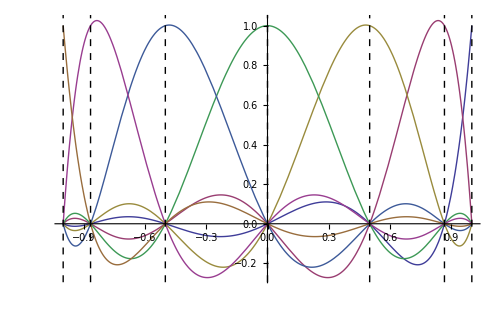

```mathematica
n=6;
x=Cos[π/n Range[0,n]]//N;
p[i_]:=If[i==0||i==n,2,1]
c[j_Integer,y_]:=2/(n  p[j])(∑_(m=0)^n 1/p[m] ChebyshevT[m, x⟦j+1⟧] ChebyshevT[m, y])
Plot[Table[c[i,y],{i,0,n}]//Evaluate,{y,-1,1},ImageSize->500,Epilog->{Black,Dashed,Line[{{#,-2},{#,2}}]&/@x}]
```

### Boundary conditions

Assuming one has done the rescaling in the previous section, there are now two solutions near the boundary, where the one we want remains finite and the other diverges. Since we represent the function as a sum of the cardinal functions (shown above), and these functions are all finite, this condition is implemented automatically by the choice of this set of basis functions.

Near the horizon the solution we want (the ingoing one) goes smoothly to a constant, while the one we do not want oscillates more and more rapidly closer to the horizon. Luckily, again our basis functions match the behaviour of the solution we want: they go smoothly to a constant. So the correct solution is automatically picked up.

Hence writing the equation in Eddington-Finkelstein coordinates and working with a Chebyshev grid will implicitly solve both boundary conditions, we do not have to worry about them further.

## Generalized Eigenvalue Equation

The simplest type of quasinormal mode equation is of the form

c_0(u,ω)ϕ(u) + c_1(u,ω)ϕ'(u)+c_2(u,ω)ϕ''(u)=0,

where each of the c_i are linear in ω: c_i(u,ω)=c_(i,0)(u)+ω c_(i,1)(u).

When we discretize the radial variable using the spectral methods as above, u becomes a vector and the derivatives are represented by matrices.

Very concretely what we do is first to collect the powers of the frequency ω in the equation. For each of these we compute the discretized coefficient of each derivative of the function ϕ, then multiply it with the corresponding derivative matrix and add them.

This brings the equation in the form

(M_0+ω M_1)ϕ=0

where the M_i are now purely numerical matrices. Explicitly,

M_(0,ij)=c_0(x_i)δ_ij+c_1(x_i)D_ij^(1)+c_2(x_i)D_ij^(2)

and similarly for M_1.

In this form the equation has become a generalized eigenvalue equation, which can be solved using Mathematica's built in function Eigenvalues.

## Extension: coupled equations, higher powers of ω

The above can be easily extended in a few directions.

Firstly, if we have a coupled system of equations, say:

c_0(u,ω)ϕ(u) + c_1(u,ω)ϕ'(u)+c_2(u,ω)ϕ''(u)=0,

d_0(u,ω)ψ(u) + d_1(u,ω)ψ'(u)+d_2(u,ω)ψ''(u)=0,

we may simply join the two functions ϕ and ψ into a single vector (ϕ,ψ) of twice the size.

We split the equation into coefficients of ω as before, but now the matrix M_0 above becomes

(M_(0, 1)(ϕ) | M_(0, 1)(ψ)
M_(0, 2)(ϕ) | M_(0, 2)(ψ))

where M_(0,1)(ϕ) is the coefficient of ϕ in the part of the first equation that contains no ω. The matrix M_1 above gets a similar modification, and we can solve the same generalized eigenvalue problem, but now with matrices of twice the size.

Further, we can generalize it to an equation which instead of linear in ω is an arbitrary polynomial in ω. Whether coupled or not, the procedure above will bring such a (system of) equation(s) in the form

(M_0+M_1 ω+M_2 ω^2+...+ M_p ω^p)ϕ=0

We can rewrite this into an equation that is linear in ω and acts on the vector (ϕ^(0),ϕ^(1),..., ϕ^(p-1)), with a matrix that looks like, for p=3:

(M_0 | M_1 | M_2+ω M_3
-ω | 1 | 0
0 | -ω | 1)

The first row represents the actual equation, while the other rows enforce that ϕ^(i)=ω^i ϕ.

Note that ϕ here might already be a combination of several functions, in the case of a coupled system of equations.

This generlizes straightforwardly to arbitrary powers of ω, with the first row representing the actual equations, and apart from that identity matrices on the main diagonal and -ω on the diagonal below the main diagonal setting ϕ^(i)=ω^i ϕ.

## References

Some excellent reviews on numerical relativity are:

P. M. Chesler and L. G. Yaffe, Numerical solution of gravitational dynamics in asymptotically anti-de Sitter spacetimes, JHEP 07 (2014) 086

O. J. C. Dias, J. E. Santos and B. Way, Numerical Methods for Finding Stationary Gravitational Solutions, (2015)

P. Grandclement and J. Novak, Spectral Methods for Numerical Relativity, Living Rev. Relativity 12 (2009)

and the standard reference on spectral methods is

J. P. Boyd, Chebyshev & Fourier Spectral Methods, Courier Dover Publications (2001)

More About

Related Tutorials

Introduction

Simple Example

Extensions

Method

Related Wolfram Education Group Courses